# LF holographic QCD

## Analytical structures of GPDs of the nucleon and pion

## Initialization

```mathematica
Clear["Global`*"];
```

```mathematica
Format[x,TraditionalForm]:=Style["x",FontColor->Blue];
Format[kt,TraditionalForm]:=Style["k_⊥",FontColor->Blue];
Format[Q,TraditionalForm]:=Style["Q",FontColor->Blue];
Format[Q2,TraditionalForm]:=Style["Q^2",FontColor->Blue];
Format[t,TraditionalForm]:=Style["t",FontColor->Blue];
Format[qt,TraditionalForm]:=Style["q_⊥",FontColor->Blue];
Format[bt,TraditionalForm]:=Style["b_⊥",FontColor->Cyan];
Format[ζ,TraditionalForm]:=Style["ζ",FontColor->Cyan];
Format[z,TraditionalForm]:=Style["z",FontColor->Cyan];
Format[mq,TraditionalForm]:=Style["m_q",FontColor->Orange];
Format[mD,TraditionalForm]:=Style["mD",FontColor->Orange];
Format[η,TraditionalForm]:=Style["η",FontColor->Orange];
Format[λ,TraditionalForm]:=Style["λ",FontColor->Orange];
Format[κ,TraditionalForm]:=Style["κ",FontColor->Orange];
Format[τ,TraditionalForm]:=Style["τ",FontColor->Magenta];
```

```mathematica
Γ=Gamma;
Β=Beta;(*Beta*)
```

## Pion

### Massless

Form factor

```mathematica
FF[Q2_,τ_,λ_]:=Γ[τ-1/2]/(√π Γ[τ-1]) Β[τ-1,Q2/(4 λ)+1/2];
```

GPD

```mathematica
u[x_]:=x Exp[x (1-x)];
GPDH[x_,Q2_,τ_,λ_]:=Γ[τ-1/2]/(√π Γ[τ-1]) u[x]^(Q2/(4 λ)-1/2)(1-u[x])^(τ-2) u'[x];
(*
GPDHα[x_,Q2_,τ_,λ_,α_]:=Γ[τ-1/2]/(√π Γ[τ-1]) (1-(1-x)^α)^(Q2/(4 λ)-1/2) α (1-x)^(α τ-α-1);
GPDHa[x_,Q2_,τ_,λ_,m_]:=Γ[τ-1/2]/(√π Γ[τ-1]) x^(Q2/(4 λ)-1/2)(1-x)^(τ-2) (x (1-x))^(4 m^2/λ);
Na[τ_?NumberQ,λ_?NumberQ,m_?NumberQ]:=NIntegrate[GPDHa[x,0,τ,λ,m],{x,0,1}];
GPDHb[x_,Q2_,τ_,λ_,m_]:=Γ[τ-1/2]/(√π Γ[τ-1]) x^(Q2/(4 λ)-1/2)(1-x)^(τ-2) Exp[-m^2/(λ x (1-x))];
Nb[τ_?NumberQ,λ_?NumberQ,m_?NumberQ]:=NIntegrate[GPDHb[x,0,τ,λ,m],{x,0,1}];
*)
```

```mathematica
λ0=0.5482^2;
```

```mathematica
FFπ[Q2_]:=(((1-γ) FF[Q2,2,λ0]+γ FF[Q2,4,λ0])/.{γ->0.125});
(*
FFπa[Q2_?NumberQ,m_?NumberQ]:=(((1-γ) NIntegrate[GPDHa[x,Q2,2,λ0,m],{x,0,1}]/Na[2,λ0,m]+γ NIntegrate[GPDHa[x,Q2,4,λ0,m],{x,0,1}]/Na[4,λ0,m])/.{γ->0.125});
FFπb[Q2_?NumberQ,m_?NumberQ]:=(((1-γ) NIntegrate[GPDHb[x,Q2,2,λ0,m],{x,0,1}]/Nb[2,λ0,m]+γ NIntegrate[GPDHb[x,Q2,4,λ0,m],{x,0,1}]/Nb[4,λ0,m])/.{γ->0.125});
*)
```

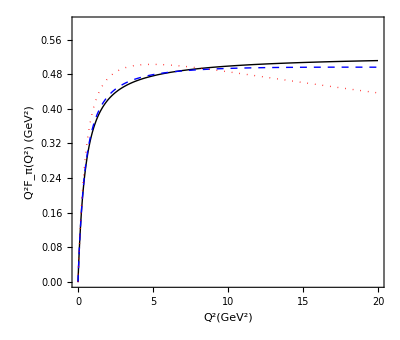

```mathematica
fig["pion FF"]=Plot[{Q2 FFπ[Q2],Q2 FFπa[Q2,0.050], Q2 FFπb[Q2,0.050]},{Q2,0,20},PlotRange->{0,0.6},Frame->True,LabelStyle->16,AspectRatio->0.85,PlotStyle->{{Black,Thick},{Blue,Dashed,Thick},{Red,Dotted,Thick}},FrameLabel->{Style["Q^2(GeV^2)",18],Style["Q^2F_π(Q^2) (GeV^2)",18]}]
```

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/notebook/pion_ff.png",fig["pion FF"]];
```

## Nucleon

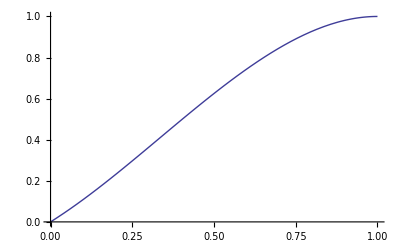

```mathematica
Plot[(a x+(3-2 a) x^2+(a-2)x^3)/.{a->1},{x,0,1}]
```

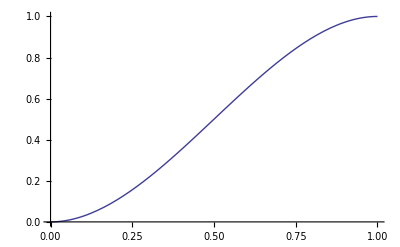

```mathematica
Plot[(1+a (1-x)^2-(1+a) (1-x)^3)/.{a->-3},{x,0,1}]
```

```mathematica
r0=1.5;
FFp[Q2_]:=FF[Q2,3,λ0];
FFpa[Q2_?NumberQ,m_?NumberQ]:=NIntegrate[GPDHa[x,Q2,3,λ0,m],{x,0,1}]/Na[3,λ0,m];
FFpb[Q2_?NumberQ,m_?NumberQ]:=NIntegrate[GPDHb[x,Q2,3,λ0,m],{x,0,1}]/Nb[3,λ0,m];
FFn[Q2_]:=-r0/3 (FF[Q2,3,λ0]-FF[Q2,4,λ0]);
FFna[Q2_?NumberQ,m_?NumberQ]:=-r0/3(NIntegrate[GPDHa[x,Q2,3,λ0,m],{x,0,1}]/Na[3,λ0,m]-NIntegrate[GPDHa[x,Q2,4,λ0,m],{x,0,1}]/Na[4,λ0,m]);
FFnb[Q2_?NumberQ,m_?NumberQ]:=-r0/3(NIntegrate[GPDHb[x,Q2,3,λ0,m],{x,0,1}]/Nb[3,λ0,m]-NIntegrate[GPDHb[x,Q2,4,λ0,m],{x,0,1}]/Nb[4,λ0,m]);
```

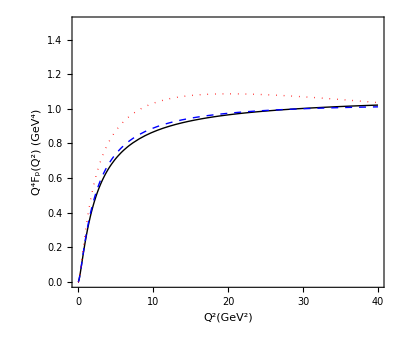

```mathematica
fig["proton FF"]=Plot[{Q2^2 FFp[Q2],Q2^2 FFpa[Q2,0.050], Q2^2 FFpb[Q2,0.050]},{Q2,0,40},PlotRange->{0,1.5},Frame->True,LabelStyle->16,AspectRatio->0.85,PlotStyle->{{Black,Thick},{Blue,Dashed,Thick},{Red,Dotted,Thick}},FrameLabel->{Style["Q^2(GeV^2)",18],Style["Q^4F_p(Q^2) (GeV^4)",18]}]
```

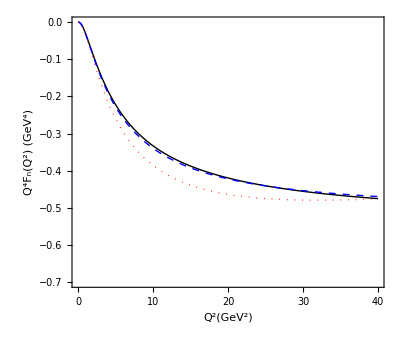

```mathematica
fig["neutron FF"]=Plot[{Q2^2 FFn[Q2],Q2^2 FFna[Q2,0.050], Q2^2 FFnb[Q2,0.050]},{Q2,0,40},PlotRange->{-0.7,0},Frame->True,LabelStyle->16,AspectRatio->0.85,PlotStyle->{{Black,Thick},{Blue,Dashed,Thick},{Red,Dotted,Thick}},FrameLabel->{Style["Q^2(GeV^2)",18],Style["Q^4F_n(Q^2) (GeV^4)",18]}]
```

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/notebook/proton_ff.png",fig["proton FF"]];
Export["/Users/user/Liu/Repos/LFHQCD/notebook/neutron_ff.png",fig["neutron FF"]];
```

## Test

```mathematica
β0=11-2/3 nf;
β1=102-38/3 nf;
```

```mathematica
α[μ_]:=((4 π)/(β0 Log[t]) (1-β1/β0^2 Log[Log[t]]/Log[t]))/.{t->μ^2/Λ^2};
```

```mathematica
NSolve[(α[t]/.{nf->5})==118/1000,t,Reals]
```

{{t→162464.}}

```mathematica
NSolve[(12 π (1-(348 Log[Log[t]])/(529 Log[t])))/(23 Log[t])==0.118,t,Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{t→162464.}}

```mathematica
α[4.2]/.{nf->5,Λ->0.226}
```

0.224715

```mathematica
NSolve[(α[4.2]/.{nf->4,Λ->Λ0})==(α[4.2]/.{nf->5,Λ->0.226}),Λ0,Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Λ0→-0.323153},{Λ0→0.323153}}

```mathematica
α[4.2]/.{nf->4,Λ->0.323}
```

0.224679

```mathematica
NSolve[(α[1.3]/.{nf->3,Λ->Λ0})==(α[1.3]/.{nf->4,Λ->0.323}),Λ0,Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Λ0→-0.36962},{Λ0→0.36962}}

```mathematica
NSolve[Log[1/x]==0.0001,x]
```

{{x→0.9999}}

```mathematica
Log[10^3*1.0]
```

6.90776

```mathematica
Integrate[x^a (1-x)^b Log[1/x],{x,0,1},Assumptions->{a>-1,b>0}]//TraditionalForm
```

-(a+1 b+1 (a-a+b+1))/(a+b+2)

```mathematica
Integrate[(x^a (1-x)^b Log[1/x]/(Beta[a+1,b+1] (PolyGamma[a+b+2]-PolyGamma[a+1])))/.{a->1/2,b->2.},{x,0,1}]
```

1.

```mathematica
N[(Beta[a+1,b+1] (PolyGamma[a+b+2]-PolyGamma[a+1]))/.{a->0.5,b->2.67}]
```

0.172906

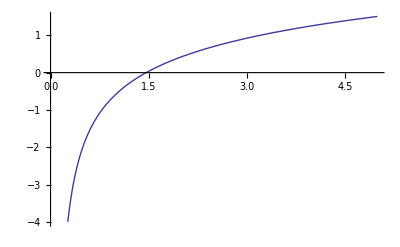

```mathematica
Plot[PolyGamma[x],{x,0,5}]
```

```mathematica
N[EulerGamma,3]
```

0.577

```mathematica
NIntegrate[(x^a (1-x)^b Log[1/x]/(Beta[a+1,b+1] (PolyGamma[a+b+1]-PolyGamma[a+1])))/.{a->0.5,b->2.67},{x,10^-4,1}]
```

1.18926

```mathematica
HarmonicNumber[1.7]-EulerGamma-PolyGamma[2.7]
```

-1.11022×10^-16

```mathematica
Integrate[Log[x],{x,0,1}]
```

-1

```mathematica
Integrate[Exp[-kt^2/(2 λ) Log[1/x]/(1-x)^2] kt,{kt,0,Infinity},Assumptions->{λ>0,x>0,x<1}]
```

-((-1+x)^2 λ)/Log[x]

```mathematica
NIntegrate[(Gamma[τ-1/2]/(√π Gamma[τ-1]) x^(-1/2)(1-x)^(τ-2) Exp[-1/λ (m1^2/x+m2^2/(1-x)) (x Log[1/x])/(1-x)])/.{τ->6,λ->0.5682^2,m1->0.2,m2->0.4},{x,0,1}]
```

0.561944

```mathematica
Integrate[Exp[-1/λ (m1^2/x+m2^2/(1-x)) (x Log[1/x])/(1-x)],{x,0,1},Assumptions->{λ>0,m1>0,m2>0}]
```

Integrate[(1/x)^(-((m2^2/(1-x)+m1^2/x) x)/((1-x) λ)),{x,0,1},Assumptions→{λ>0,m1>0,m2>0}]

```mathematica
Integrate[Gamma[τ-1/2]/(√π Gamma[τ-1]) x^(-1/2)(1-x)^(τ-2) ,{x,0,1},Assumptions->{τ>1}]
```

1

```mathematica
Sqrt[10.]
```

3.16228

```mathematica
ϕ[x_,σ_,μ_]:=1/(√(2 π))Exp[-1/(2 σ^2)(x-μ)^2];
```

```mathematica
Integrate[ϕ[x,1,0],{x,-k,k}]/.{k->1.7}
```

0.910869

```mathematica
Integrate[x^(α-1) (1-x)^β+γ (2 x^2)/(9 M^2),{x,0,1},Assumptions->{α>0,β>0}]
```

(2 γ)/(27 M^2)+(Gamma[α] Gamma[1+β])/Gamma[1+α+β]

```mathematica
v[x_,α_,β_,γ_]:=(x^α (1-x)^β+γ (2 x^2)/(9 M^2))/((2 γ)/(27 M^2)+Beta[α,1+β])
```

```mathematica
(D[v[x,α,β,γ],α]//FullSimplify)//TraditionalForm
```

(27 M^2 (x^α (1-x)^β (27 M^2 αβ+1 (0α+β+1-0α+log(x))+2 γ log(x))+6 γ x^2 (0α+β+1-0α) αβ+1))/((2 γ+27 M^2 αβ+1)^2)

```mathematica
Integrate[(v[x,α,β,γ])/.{α->0.70,β->1.54,γ->0.60,M->5.2},{x,0,1}]
```

0.217877

```mathematica
fs=OpenWrite["/Users/user/Desktop/hoppet-1.1.5/mycode/results/pion_parameterization_Q=5.2.dat"];
WriteString[fs,"PRC72(2005)065203 prefered parameterization Q=5.2GeV\n"];
WriteString[fs,"x\txv\tdxv\n"];
sep="  ";
For[i=0,i<1000,i++,
x0=0.0005+0.001 i;
xv=v[x0,0.70,1.54,0.60]/.{M->5.2};
dxv2=((D[v[x,α,β,γ],α])^2 0.06^2+(D[v[x,α,β,γ],β])^2 0.08^2+(D[v[x,α,β,γ],γ])^2 0.34^2)/.{x->x0,α->0.70,β->1.54,γ->0.60,M->5.2};
WriteString[fs,x0,"\t",N[xv,6],"\t",N[Sqrt[dxv2],6],"\n"]
];
Close[fs];
```

```mathematica
α
```

α

```mathematica
Clear[fs]
```

```mathematica
afd
```

```mathematica
FX[x_]:=x^(-1/2) ((1-γ)/2+15/16 γ (1-x)^2) (x (1-x))^η;
```

```mathematica
Integrate[FX[x],{x,0,1},Assumptions->{η>0}]
```

(4^(-2-η) √π (30+η (32 (2+η)-γ (19+17 η))) Gamma[1+2 η])/Gamma[7/2+2 η]

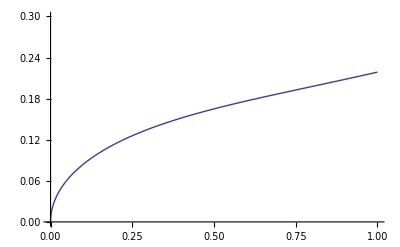

```mathematica
Plot[(x^(1/2)/2 ((1-γ)/2+15/16 γ (1-x)^2))/.{γ->0.125},{x,0,1},PlotRange->{0,0.3}]
```

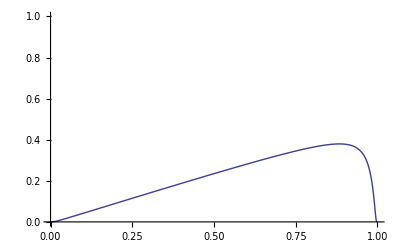

```mathematica
Plot[(x/2 Exp[-m^2/(x (1-x))])/.{m->0.125},{x,0,1},PlotRange->{0,1}]
```

```mathematica
Integrate[1/1.193(x^(α-1) (1-x)^β (1+γ x^2))/.{α->0.7,β->2.03,γ->13.8},{x,0,1}]
```

1.00011